```mathematica
Quit
```

```mathematica
(* Test 1 *)
```

```mathematica
HMD[a_]:=√(Ω a^-3)
Geff[a_,ga_,m1_]:=1+ga (1-a)^m1-ga (1-a)^(2m1)
```

```mathematica
Series[Geff[a,ga,2],{a,0,2}]
```

1+2 ga a-5 ga a^2+O[a]^3

```mathematica
Geffapp[a_]:=1+2 ga a
ode=d''[a]+(3/a+HMD'[a]/HMD[a])d'[a]-3/2(Ω Geffapp[a])/(a^5 HMD[a]^2)d[a]//Simplify
```

-(3 (1+2 a ga) d[a])/(2 a^2)+(3 d'[a])/(2 a)+d''[a]

```mathematica
dsol=DSolve[ode==0,d[a],a][[1]]
```

{d[a]→(ⅇ^(2 √3 √a √ga) (1-2 √3 √a √ga+4 a ga) C[1])/a^(3/2)-(ⅇ^(-2 √3 √a √ga) (√3+6 √a √ga+4 √3 a ga) C[2])/(96 a^(3/2) ga^(5/2))}

```mathematica
ss=Series[dsol[[1,2]],{a,0,4}]//FullSimplify
```

(C[1]-C[2]/(32 √3 ga^(5/2)))/a^(3/2)+(-2 ga C[1]+C[2]/(16 √3 ga^(3/2)))/(√a)+(6 ga^2 C[1]-(√3 C[2])/(16 √ga)) √a+1/5 (32 √3 ga^(5/2) C[1]+C[2]) a+(12 ga^3 C[1]-1/8 √3 √ga C[2]) a^(3/2)+6/35 ga (32 √3 ga^(5/2) C[1]+C[2]) a^2+(6 ga^4 C[1]-1/16 √3 ga^(3/2) C[2]) a^(5/2)+2/35 ga^2 (32 √3 ga^(5/2) C[1]+C[2]) a^3+3/200 (96 ga^5 C[1]-√3 ga^(5/2) C[2]) a^(7/2)+4/385 ga^3 (32 √3 ga^(5/2) C[1]+C[2]) a^4+(3 (96 ga^6 C[1]-√3 ga^(7/2) C[2]) a^(9/2))/1400+O[a]^5

```mathematica
solc1=Solve[SeriesCoefficient[ss,-3/2]==0,C[1]][[1]]
```

{C[1]→C[2]/(32 √3 ga^(5/2))}

```mathematica
δwCDM[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[a_,w_,Ω_]:=aa D[Log[δwCDM[aa,w,Ω]],aa]/.aa->a
fσ8wCDM[a_,w_,Ω_,σ8_]:=fwCDM[a,w,Ω]σ8  δwCDM[a,w,Ω]/δwCDM[1,w,Ω]
```

```mathematica
Series[δwCDM[a,-1,Ω],{a,0,4}]
```

a+(2 (-1+Ω) a^4)/(11 Ω)+O[a]^5

```mathematica
ss/.solc1/.C[2]->5/2
```

a+(6 ga a^2)/7+(2 ga^2 a^3)/7+(4 ga^3 a^4)/77+O[a]^5

```mathematica
δa=d[a]/.dsol/.solc1/.C[2]->5/2//FullSimplify
```

(5 (-6 √a √ga Cosh[2 √3 √a √ga]+√3 (1+4 a ga) Sinh[2 √3 √a √ga]))/(96 a^(3/2) ga^(5/2))

```mathematica
ga0=-0.627;
σa0=-3.562;
m10=2;
m20=2;
om0=0.3;
σ80=0.8;
HwCDM[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)))
H[a_]:=HwCDM[a,-1,om0]
```

```mathematica
sol1=NDSolve[{d''[a]+(3/a+H'[a]/H[a])d'[a]-3/2(om0 Geff[a,ga0,m10])/(a^5 H[a]^2)d[a]==0,d[0.001]==0.001,d'[0.001]==1,f[a]==a d'[a]/d[a],f[0.001]==1},{d[a],f[a]},{a,0.001,1}]//Quiet;
```

```mathematica
{δa/.ga->ga0//Re,d[a]/.sol1[[1]]}/.a->0.01
```

{0.00994637,0.00995436}

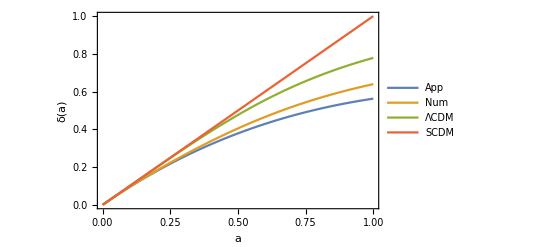

```mathematica
Plot[{δa/.ga->ga0//Re,d[a]/.sol1[[1]],δwCDM[a,-1,om0],δwCDM[a,-1,1]},{a,0.001,1},PlotLegends->{"App","Num","ΛCDM","SCDM"},Frame->True,FrameLabel->{"a","δ(a)"},FrameStyle->Black]
```

```mathematica
(* fσ8 GA fit *)
off=0.9950027651950218;
fσ8GA0[X_]:=-3/2 (0.2964540316820736-0.6107583160457111 ⅇ^(-32.65140939370555 X)+0.21136617943906222 ⅇ^(-8.00203709332559 X)+0.8475957992148122 ⅇ^(-2.025807037607944 X)) X;
fσ8GAa[a_]:=fσ8GA0[x]/.x->a^3;
fσ8GA[a_]:=a(off+fσ8GAa[a])
fGA[a_?NumericQ]:=fσ8GA[a]/NIntegrate[fσ8GA[x]/x,{x,0,a}]
```

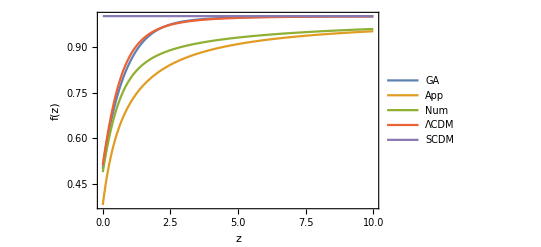

```mathematica
Plot[{fGA[a],a D[δa,a]/δa/.ga->ga0//Re,f[a]/.sol1[[1]],fwCDM[a,-1,om0],fwCDM[a,-1,1]}/.a->1/(1+z)//Evaluate,{z,0,10},PlotLegends->{"GA","App","Num","ΛCDM","SCDM"},Frame->True,FrameLabel->{"z","f(z)"},FrameStyle->Black,PlotRange->All]
```

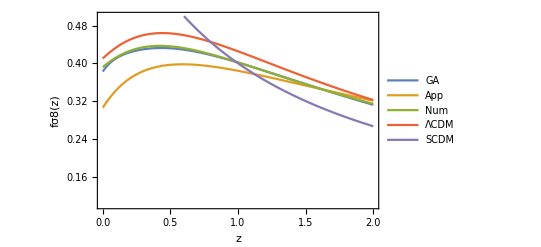

```mathematica
Plot[{fσ8GA[a],σ80 a D[δa,a]/(δa/.a->1)/.ga->ga0//Re,σ80 (f[a]d[a]/.sol1[[1]])/(d[a]/.sol1[[1]]/.a->1),fσ8wCDM[a,-1,om0,σ80],fσ8wCDM[a,-1,1,σ80]}/.a->1/(1+z)//Evaluate,{z,0,2},PlotLegends->{"GA","App","Num","ΛCDM","SCDM"},Frame->True,FrameLabel->{"z","fσ8(z)"},FrameStyle->Black,PlotRange->{0.1,0.5}]
```

```mathematica
(* end *)
```

```mathematica
(* Test 2 *)
```

```mathematica
HMD[a_]:=√(Ω a^-3)
Geff[a_,ga_,m1_]:=1+ga (1-a)^m1-ga (1-a)^(2m1)
```

```mathematica
Series[Geff[a,ga,2],{a,1,2}]
```

1+ga (a-1)^2+O[a-1]^3

```mathematica
Geffapp[a_]:=1+ga (a-1)^2
ode=d''[a]+(3/a+HMD'[a]/HMD[a])d'[a]-3/2(Ω Geffapp[a])/(a^5 HMD[a]^2)d[a]//Simplify
```

-(3 (1+(-1+a)^2 ga) d[a])/(2 a^2)+(3 d'[a])/(2 a)+d''[a]

```mathematica
dsol=DSolve[ode==0,d[a],a][[1]]//FullSimplify
```

{d[a]→a^(1/4 (-1+√(25+24 ga))) ⅇ^(-√(3/2) a √ga) (C[1] HypergeometricU[1/4 (2-2 √6 √ga+√(25+24 ga)),1/2 (2+√(25+24 ga)),√6 a √ga]+C[2] LaguerreL[1/4 (-2+2 √6 √ga-√(25+24 ga)),1/2 √(25+24 ga),√6 a √ga])}

```mathematica
ics={C[1]->0,C[2]->1/LaguerreL[1/4 (-2+2 √6 √ga-√(25+24 ga)),1/2 √(25+24 ga),0]};
ss=Series[dsol[[1,2]],{a,0,0}]/.Arg[a]->0/.Arg[ga]->Pi/.ics//Normal//Expand
ss/.ga->0
```

a^(-1/4+1/4 √(25+24 ga))-√(3/2) a^(3/4+1/4 √(25+24 ga)) √ga-(√6 a^(3/4+1/4 √(25+24 ga)) √ga LaguerreL[-1+1/4 (-2+2 √6 √ga-√(25+24 ga)),1+1/2 √(25+24 ga),0])/LaguerreL[1/4 (-2+2 √6 √ga-√(25+24 ga)),1/2 √(25+24 ga),0]

a

```mathematica
Plot[dsol[[1,2]]/.ics/.ga->-0.625//Chop,{a,0,1}]
```

```mathematica
δwCDM[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
```

```mathematica
Series[δwCDM[a,-1,Ω],{a,0,4}]
```

a+(2 (-1+Ω) a^4)/(11 Ω)+O[a]^5

```mathematica
ss/.ics//FullSimplify
```

(a^(1/4 (-1+√(25+24 ga))) (2-6 a ga+√(25+24 ga)))/(2+√(25+24 ga))

```mathematica
δa=d[a]/.dsol/.ics//FullSimplify
```

a^(1/4 (-1+√(25+24 ga))) ⅇ^(-√(3/2) a √ga) Hypergeometric1F1[1/4 (2-2 √6 √ga+√(25+24 ga)),1/2 (2+√(25+24 ga)),√6 a √ga]

```mathematica
ga0=-0.627;
σa0=-3.562;
m10=2;
m20=2;
om0=0.3;
σ80=0.8;
HwCDM[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)))
H[a_]:=HwCDM[a,-1,om0]
```

```mathematica
sol1=NDSolve[{d''[a]+(3/a+H'[a]/H[a])d'[a]-3/2(om0 Geff[a,ga0,m10])/(a^5 H[a]^2)d[a]==0,d[0.001]==0.001,d'[0.001]==1,f[a]==a d'[a]/d[a],f[0.001]==1},{d[a],f[a]},{a,0.001,1}]//Quiet;
```

```mathematica
{δa/.ga->ga0//Re,d[a]/.sol1[[1]]}/.a->0.01
```

{0.0842987,0.00995436}

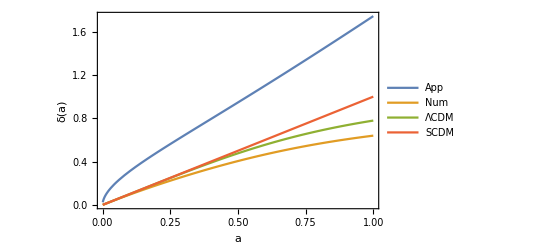

```mathematica
Plot[{δa/.ga->ga0//Re,d[a]/.sol1[[1]],δwCDM[a,-1,om0],δwCDM[a,-1,1]},{a,0.001,1},PlotLegends->{"App","Num","ΛCDM","SCDM"},Frame->True,FrameLabel->{"a","δ(a)"},FrameStyle->Black]
```

```mathematica
(* end *)
```